## Setup

```mathematica
R=10;
n=11;
h=R/(n-1)
```

1

```mathematica
symm[i_]=If[i>=1,i,2-i];
```

```mathematica
(grad2=1/h Table[
(If[j==symm[i-1],-1,0]+
If[j==symm[i+1],+1,0])/2,
{i,n},{j,n}])//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1/2 | 0)

```mathematica
(grad4=1/h Table[
(If[j==symm[i-2],+1,0]+
If[j==symm[i-1],-8,0]+
If[j==symm[i+1],+8,0]+
If[j==symm[i+2],-1,0])/12,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad6=1/h Table[
(If[j==symm[i-3],-1,0]+
If[j==symm[i-2],+9,0]+
If[j==symm[i-1],-180/4,0]+
If[j==symm[i+1],180/4,0]+
If[j==symm[i+2],-9,0]+
If[j==symm[i+3],+1,0])/60,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(grad8=1/h Table[
(     If[j==symm[i-4],+1,0]+
If[j==symm[i-3],-(280*4)/105,0]+
If[j==symm[i-2],+280/5,0]+
If[j==symm[i-1],-280*4/5,0]+
If[j==symm[i+1],+280*4/5,0]+
If[j==symm[i+2],-280/5,0]+
If[j==symm[i+3],+(280*4)/105,0]+
If[j==symm[i+4],-1,0])/280,
{i,n},{j,n}])//MatrixForm;
```

```mathematica
(W=h DiagonalMatrix[
Table[If[i==1,1/2,1],
{i,n}]
])//MatrixForm;
```

```mathematica
(B=DiagonalMatrix[Table[0,{i,n}]])//MatrixForm;
B[[n,n]]=0;
B//MatrixForm;
```

```mathematica
(div2=Inverse[W].Transpose[B-W.grad2])//MatrixForm;
(div4=Inverse[W].Transpose[B-W.grad4])//MatrixForm;
(div6=Inverse[W].Transpose[B-W.grad6])//MatrixForm;
(div8=Inverse[W].Transpose[B-W.grad8])//MatrixForm;
```

```mathematica
(QV=DiagonalMatrix[Table[q[i],{i,n}]])//MatrixForm;
```

```mathematica
(c=Table[1,{i,n}])//MatrixForm;
```

```mathematica
(r=h Table[i-1,{i,n}])//MatrixForm;
div2.r-1
grad2.r^2-2r
div4.r^3-3 r^2
grad4.r^4-4 r^3
div6.r
```

{0,0,0,0,0,0,0,0,0,0,-11/2}

{0,0,0,0,0,0,0,0,0,0,-121/2}

{0,0,0,0,0,0,0,0,0,1331/12,-2230/3}

{0,0,0,0,0,0,0,0,0,14641/12,-24098/3}

{1,1,1,1,1,1,1,1,49/60,49/20,-17/3}

```mathematica
l=0;
kk=Join[{0},Table[BesselJZero[1/2 (1+2 l),i]/R,{i,1,n-1}]];
λ=-N[kk^2];
plot0=Plot[λ,{x,.2,1},PlotStyle->Red,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

## 2nd Order

(q[1.]→0.497512
q[2.]→1.49254
q[3.]→4.47761
q[4.]→9.45274
q[5.]→16.4179
q[6.]→25.3731
q[7.]→36.3184
q[8.]→49.2537
q[9.]→64.1791
q[10.]→81.0945
q[11.]→100.)

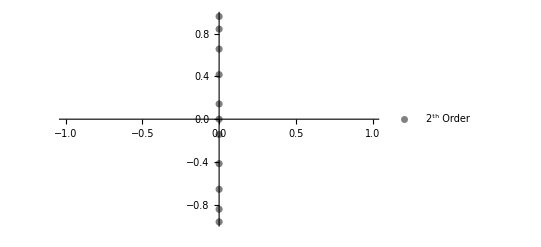

```mathematica
(cond2=div2.QV.r-3QV.c)//MatrixForm;
cond22=Join[cond2[[1;;-2]],{q[n]-r[[n]]^2}];
(sol2=Solve[cond22==0,Table[q[i],{i,n}]][[1]])//MatrixForm//N
QQV2=QV/.sol2;
DDIV2=Inverse[QQV2].div2.QQV2;
DDIV2.r//FullSimplify;
(vals2=Eigenvalues[DDIV2])//N//MatrixForm;
cplot2=ComplexListPlot[vals2,AspectRatio->1/GoldenRatio,PlotStyle->Gray,PlotLegends->{"2^th Order"},PlotRange->All]
```

## 4th Order

```mathematica
order=3;
```

```mathematica
(QS4= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i,q[i,j],
j<i,q[j,i],
True,0],
True,0],{i,n},{j,n}]
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | q[4] | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5] | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11])

```mathematica
(cond4a=div4.QV.r-3QS4.c)//MatrixForm;
(cond4b=div4.QV.r^3-5QS4.r^2)//MatrixForm;
```

```mathematica
(*(cond4=Join[
cond4a[[;;-3]],
cond4b[[;;3]],
{q[1]-100/201,q[2]-100/67(*,q[3]-300/67*)(*,q[4]-1900/201,q[5]-1100/67,q[5]-1100/67,q[6]-1700/67,q[7]-7300/201,
q[8]-3300/67,q[9]-4300/67,*)(*q[n-2]-r[[n-2]]^2,q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2*)}])//MatrixForm;*)
```

```mathematica
(cond4=Join[
cond4a[[;;-3]],
cond4b[[;;3]],
{(*q[1]-2/3,*)
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;
(vars4 = DeleteDuplicates[SparseArray[QS4]["NonzeroValues"]])//MatrixForm;
(*RealQ[x_]:=!(Element[x,Reals]===True)
vars =Select[vars,RealQ];*)
Length[vars4]
Length[cond4]
```

14

14

```mathematica
(solq4=Solve[cond4==0,vars4][[1]])//MatrixForm//N
```

(q[1.]→2.24546
q[1.,2.]→-1.57314
q[1.,3.]→0.347464
q[2.]→3.28846
q[2.,3.]→-0.794056
q[3.]→3.97578
q[4.]→9.05287
q[5.]→15.9776
q[6.]→25.0114
q[7.]→35.9908
q[8.]→49.003
q[9.]→63.9939
q[10.]→81.
q[11.]→100.)

```mathematica
(QQS4 = QS4/.solq4)//MatrixForm//N;
QQV4=QV/.solq4;
```

```mathematica
PositiveDefiniteMatrixQ[QQS4]
```

True

```mathematica
(DDIV4 = Inverse[QQS4].div4.QQV4)//N//MatrixForm
```

(0. | 2.83674 | 0.409221 | -0.208211 | -0.00763764 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.13546 | 1.04346 | 0.0440527 | -0.0886335 | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.572554 | 0.172639 | 1.545 | -0.35193 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.0302709 | -0.292782 | 0. | 1.17662 | -0.230235 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.0207362 | -0.377731 | 0. | 1.0436 | -0.187714 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.0301624 | -0.425876 | 0. | 0.959316 | -0.163269 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0369947 | -0.463293 | 0. | 0.907694 | -0.148172 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.0425339 | -0.489641 | 0. | 0.870612 | -0.137747 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0468675 | -0.510496 | 0. | 0.843831 | -0.130221
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0504146 | -0.526698 | 0. | 0.823045
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0533282 | -0.54 | 0.)

```mathematica
DDIV4.r//FullSimplify//MatrixForm//N
```

(3.
3.
3.
3.
3.
3.
3.
3.
3.
4.36977
-4.43337)

```mathematica
(DDIV4.r^3-5 r^2)[[;;5]]//FullSimplify//MatrixForm//N
```

(0.
0.
0.
-0.787856
-0.128988)

```mathematica
(vals4=Eigenvalues[N[DDIV4]])//MatrixForm
```

(0.012976+1.30004 ⅈ
0.012976-1.30004 ⅈ
0.0488277+1.09615 ⅈ
0.0488277-1.09615 ⅈ
0.100264+0.793705 ⅈ
0.100264-0.793705 ⅈ
0.160952+0.431543 ⅈ
0.160952-0.431543 ⅈ
0.434788+0. ⅈ
0.227273+0. ⅈ
0.+0. ⅈ)

```mathematica
SpectralRadius=Max[Norm[vals4]]
```

2.7809

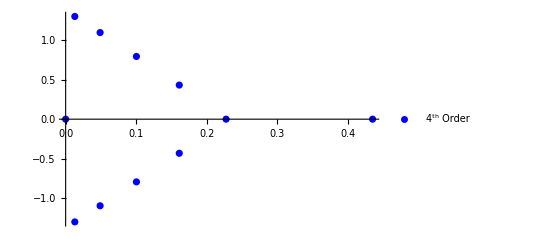

```mathematica
cplot4=ComplexListPlot[vals4,AspectRatio->1/GoldenRatio, PlotStyle->Blue, PlotLegends->{"4^th Order"},PlotRange->All]
```

```mathematica
(lvals4=Sort[Eigenvalues[N[DDIV4.grad4]]])//MatrixForm
```

(-2.66327
-1.79364
-1.69222
-1.33812
-1.16785
-0.7943
-0.627242
-0.385554
-0.26316
-0.113283
4.07472×10^-16)

```mathematica
(λ[[-1]]/lvals4[[1]])
```

3.70582

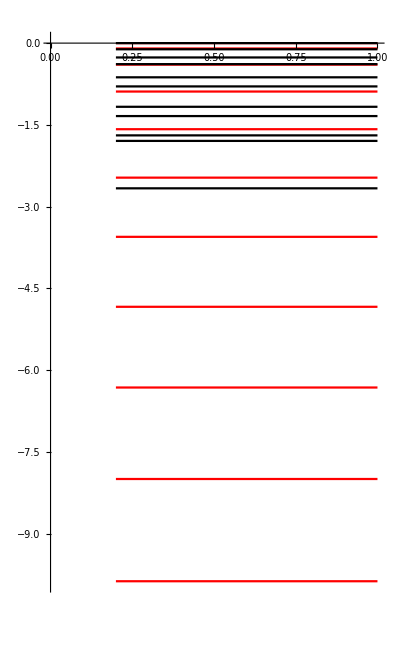

```mathematica
plot4=Plot[lvals4,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},All},PlotLabel->"6th Order"];
Show[plot0, plot4]
```

## 6th Order

```mathematica
order=5;
(QS6= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i+1,q[i,j],
j<i-1,q[j,i],
True,0],
True,0],{i,n},{j,n}]
+Table[If[i≤n-2&& j≤n-2,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | q[2,4] | q[2,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | q[3,4] | q[3,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | q[4] | q[4,5] | 0 | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | q[5] | q[5,6] | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5,6] | q[6] | q[6,7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | q[6,7] | q[7] | q[7,8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | q[7,8] | q[8] | q[8,9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8,9] | q[9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11])

```mathematica
QS6=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], q[5], q[5,6], q[5,7], 0, 0, 0, 0}, {0, 0, 0, q[4,6], q[5,6], q[6], q[6,7], q[6,8], 0, 0, 0}, {0, 0, 0, 0, q[5,7], q[6,7], q[7], q[7,8], 0, 0, 0}, {0, 0, 0, 0, 0, q[6,8], q[7,8], q[8], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11]}});
```

```mathematica
(cond6a=div6.QV.r-3QS6.c)//MatrixForm;
(cond6b=div6.QV.r^3-5QS6.r^2)//MatrixForm;
(cond6c=div6.QV.r^5-7QS6.r^4)//MatrixForm;
(cond6d=div6.QV.r^7-9QS6.r^6)//MatrixForm;
```

```mathematica
(*(cond6=Join[
cond6a[[;;-4]],
cond6b[[;;-4]],
cond6c[[;;5]],
{q[n-2]-r[[n-2]]^2,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;*)
(* this produces the same spectrum as the 4th order!
QS6=({{q[1], q[1,2], q[1,3], q[1,4], 0, 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], q[3,6], 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], 0, 0, 0, 0, 0}, {0, q[2,5], q[3,5], q[4,5], q[5], q[5,6], 0, 0, 0, 0, 0}, {0, 0, q[3,6], q[4,6], q[5,6], q[6], q[6,7], 0, 0, 0, 0}, {0, 0, 0, 0, 0, q[6,7], q[7], q[7,8], 0, 0, 0}, {0, 0, 0, 0, 0, 0, q[7,8], q[8], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11]}});
(cond6=Join[
cond6a[[;;-4]],
cond6b[[;;-4]],
cond6c[[;;6]],
{q[n-2]-r[[n-2]]^2,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;*)
```

```mathematica
(cond6=Join[
cond6a[[;;-4]],
cond6b[[;;-4]],
cond6c[[;;7]],
{q[1]-2/3,
q[n-2]-r[[n-2]]^2,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}])//MatrixForm;
(vars6 = DeleteDuplicates[SparseArray[QS6]["NonzeroValues"]])//MatrixForm;
(*RealQ[x_]:=!(Element[x,Reals]===True)
vars =Select[vars,RealQ];*)
Length[vars6]
Length[cond6]
```

27

27

```mathematica
(solq6=Solve[cond6==0,vars6][[1]])//MatrixForm//N
```

(q[1.]→0.666667
q[1.,2.]→-0.439132
q[1.,3.]→0.401604
q[1.,4.]→-0.232319
q[1.,5.]→0.069384
q[2.]→2.02058
q[2.,3.]→-0.843876
q[2.,4.]→0.37794
q[2.,5.]→-0.0456005
q[3.]→4.19741
q[3.,4.]→-0.148195
q[3.,5.]→0.0461115
q[4.]→8.86189
q[4.,5.]→0.0669103
q[4.,6.]→-0.00478473
q[5.]→15.9696
q[5.,6.]→0.0102571
q[5.,7.]→0.00416718
q[6.]→25.0012
q[6.,7.]→-0.0165777
q[6.,8.]→0.00939511
q[7.]→35.9936
q[7.,8.]→0.00567129
q[8.]→48.9955
q[9.]→64.
q[10.]→81.
q[11.]→100.)

```mathematica
(QQS6 = QS6/.solq6)//MatrixForm//N
QQV6=QV/.solq6;
```

(0.666667 | -0.439132 | 0.401604 | -0.232319 | 0.069384 | 0. | 0. | 0. | 0. | 0. | 0.
-0.439132 | 2.02058 | -0.843876 | 0.37794 | -0.0456005 | 0. | 0. | 0. | 0. | 0. | 0.
0.401604 | -0.843876 | 4.19741 | -0.148195 | 0.0461115 | 0. | 0. | 0. | 0. | 0. | 0.
-0.232319 | 0.37794 | -0.148195 | 8.86189 | 0.0669103 | -0.00478473 | 0. | 0. | 0. | 0. | 0.
0.069384 | -0.0456005 | 0.0461115 | 0.0669103 | 15.9696 | 0.0102571 | 0.00416718 | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.00478473 | 0.0102571 | 25.0012 | -0.0165777 | 0.00939511 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.00416718 | -0.0165777 | 35.9936 | 0.00567129 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.00939511 | 0.00567129 | 48.9955 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 64. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100.)

```mathematica
PositiveDefiniteMatrixQ[QQS6]
```

True

```mathematica
(DDIV6 = Inverse[QQS6].div6.QQV6)//MatrixForm;
```

```mathematica
DDIV6.r//FullSimplify//MatrixForm//N
```

(3.
3.
3.
3.
3.
3.
3.
3.
2.65366
5.10921
-4.75666)

```mathematica
(DDIV6.r^3-5 r^2)//FullSimplify//MatrixForm//N
```

(0.
0.
0.
0.
0.
0.
0.
0.
-41.9255
247.04
-896.516)

```mathematica
(DDIV6.r^5-7 r^4)//FullSimplify//MatrixForm//N
```

(-1.00754×10^-7
3.31675×10^-8
3.9826×10^-9
-2.4521×10^-7
3.33914×10^-7
-0.0004421
-0.00018552
1.17614
-5073.45
28714.9
-102864.)

```mathematica
(vals6=Eigenvalues[N[DDIV6]])//MatrixForm
```

(0.0750927+1.51254 ⅈ
0.0750927-1.51254 ⅈ
0.120581+1.38275 ⅈ
0.120581-1.38275 ⅈ
0.115546+1.04182 ⅈ
0.115546-1.04182 ⅈ
0.128418+0.635749 ⅈ
0.128418-0.635749 ⅈ
0.135719+0.213254 ⅈ
0.135719-0.213254 ⅈ
0.+0. ⅈ)

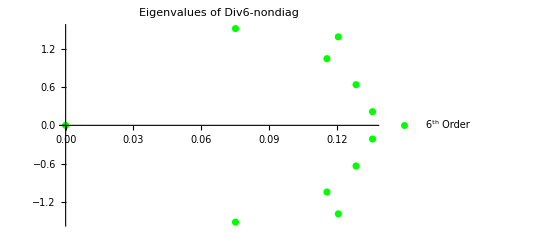

```mathematica
cplot6=ComplexListPlot[vals6,AspectRatio->1/GoldenRatio,PlotRange->All, PlotLabel->"Eigenvalues of Div6-nondiag",PlotStyle->Green,PlotLegends->{"6^th Order"}]
```

```mathematica
(lvals6=Sort[Eigenvalues[N[DDIV6.grad6]]])//MatrixForm
```

(-5.17792
-2.46243
-2.28116
-1.86205
-1.57628
-1.15551
-0.882301
-0.554001
-0.344707
-0.127715
1.50049×10^-16)

```mathematica
(λ[[-1]]/lvals6[[1]])
```

1.90609

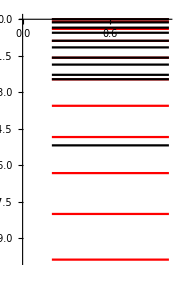

```mathematica
plot6=Plot[lvals6(**(λ[[-1]]/lvals6[[1]])*),{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},All},PlotLabel->"6th Order"];
Show[plot0, plot6]
```

## 8th Order

```mathematica
order=6;
(QS8= QV
+Table[Which[i≤order&&j≤order,
Which[
j>i+2,q[i,j],
j<i-2,q[j,i],
True,0],
True,0],{i,n},{j,n}]
+Table[If[i≤n-4&& j≤n-4,Which[j==i+1,q[i,j],j==i-1,q[j,i],True,0],0],{i,n},{j,n}]
+Table[If[i≤n-4&& j≤n-4,Which[j==i+2,q[i,j],j==i-2,q[j,i],True,0],0],{i,n},{j,n}]
)//MatrixForm
```

(q[1] | q[1,2] | q[1,3] | q[1,4] | q[1,5] | q[1,6] | 0 | 0 | 0 | 0 | 0
q[1,2] | q[2] | q[2,3] | q[2,4] | q[2,5] | q[2,6] | 0 | 0 | 0 | 0 | 0
q[1,3] | q[2,3] | q[3] | q[3,4] | q[3,5] | q[3,6] | 0 | 0 | 0 | 0 | 0
q[1,4] | q[2,4] | q[3,4] | q[4] | q[4,5] | q[4,6] | 0 | 0 | 0 | 0 | 0
q[1,5] | q[2,5] | q[3,5] | q[4,5] | q[5] | q[5,6] | q[5,7] | 0 | 0 | 0 | 0
q[1,6] | q[2,6] | q[3,6] | q[4,6] | q[5,6] | q[6] | q[6,7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | q[5,7] | q[6,7] | q[7] | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | q[8] | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[9] | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[10] | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | q[11])

```mathematica
(*QS8=({{q[1], q[1,2], q[1,3], q[1,4], q[1,5], q[1,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,2], q[2], q[2,3], q[2,4], q[2,5], q[2,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,3], q[2,3], q[3], q[3,4], q[3,5], q[3,6], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,4], q[2,4], q[3,4], q[4], q[4,5], q[4,6], q[4,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,5], q[2,5], q[3,5], q[4,5], q[5], q[5,6], q[5,7], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {q[1,6], q[2,6], q[3,6], q[4,6], q[5,6], q[6], q[6,7], q[6,8], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, q[4,7], q[5,7], q[6,7], q[7], q[7,8], q[7,9], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, q[6,8], q[7,8], q[8], q[8,9], q[8,10], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, q[7,9], q[8,9], q[9], q[9,10], q[9,11], 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, q[8,10], q[9,10], q[10], q[10,11], q[10,12], 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, q[9,11], q[10,11], q[11], q[11,12], q[11,13], 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, q[10,12], q[11,12], q[12], q[12,13], q[12,14], 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[11,13], q[12,13], q[13], q[13,14], q[13,15], 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[12,14], q[13,14], q[14], q[14,15], q[14,16], 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[13,15], q[14,15], q[15], q[15,16], q[15,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[14,16], q[15,16], q[16], q[16,17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[15,17], q[16,17], q[17], 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[18], 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[19], 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[20], 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, q[21]}})*)
```

```mathematica
(cond8a=div8.QV.r^1-3QS8.c)//MatrixForm;
(cond8b=div8.QV.r^3-5QS8.r^2)//MatrixForm;
(cond8c=div8.QV.r^5-7QS8.r^4)//MatrixForm;
(cond8d=div8.QV.r^7-9QS8.r^6)//MatrixForm;
```

```mathematica
G[q1_]:=
Module[{u},
cond8G=Join[
cond8a[[;;-5]],
cond8b[[;;-5]],
cond8c[[;;-5]],
cond8d[[;;4]],
{q[1]-q1,
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}
];vars8G = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]];solq8G=Solve[cond8G==0,vars8G][[1]];QQS8G = QS8/.solq8G;QQV8G=QV/.solq8G;DDIV8G= N[Inverse[QQS8G].div8.QQV8G];((DDIV8G.r^7-9.0 r^6)[[1]])^2]
```

```mathematica
(*q1sol=NMinimize[{G[k],k≥0.0,k≤1},k]*)
```

```mathematica
(*FindMinimum[{G[k],k≥0.0,k≤1},{k,100419445/108274511 h^2}]*)
```

```mathematica
(*q10=q1sol[[2]][[1]]// Values;*)
```

```mathematica
(*q1Rational = Rationalize[N[q10],10^-16]*)
```

```mathematica
(cond8=Join[
cond8a[[;;-5]],
cond8b[[;;-5]],
cond8c[[;;-5]],
cond8d[[;;4]],
{(*q[1]-2045027588481283/2251799813685248,*)
(*q[1]-q1Rational,*)
q[1]-h^2,
(*q[n-2]-r[[n-2]]^2,*)
q[n-1]-r[[n-1]]^2,
q[n]-r[[n]]^2}
])//MatrixForm;
(vars8 = DeleteDuplicates[SparseArray[QS8]["NonzeroValues"]])//MatrixForm;
Length[vars8]
Length[cond8]
```

28

28

```mathematica
(solq8=Solve[cond8==0,vars8][[1]])//MatrixForm//N
```

(q[1.]→1.
q[1.,2.]→-0.724265
q[1.,3.]→0.271071
q[1.,4.]→0.078496
q[1.,5.]→-0.0445297
q[1.,6.]→0.00276256
q[2.]→1.98113
q[2.,3.]→-0.511373
q[2.,4.]→0.00874003
q[2.,5.]→0.0861923
q[2.,6.]→-0.0246347
q[3.]→3.73099
q[3.,4.]→0.214236
q[3.,5.]→-0.086948
q[3.,6.]→0.00726786
q[4.]→8.85294
q[4.,5.]→0.112777
q[4.,6.]→-0.0257195
q[5.]→16.0279
q[5.,6.]→-0.0590377
q[5.,7.]→0.0201376
q[6.]→24.9752
q[6.,7.]→-0.00318796
q[7.]→35.9379
q[8.]→48.947
q[9.]→63.9843
q[10.]→81.
q[11.]→100.)

```mathematica
(QQS8 = QS8/.solq8)//MatrixForm//N
QQV8=QV/.solq8;
```

(1. | -0.724265 | 0.271071 | 0.078496 | -0.0445297 | 0.00276256 | 0. | 0. | 0. | 0. | 0.
-0.724265 | 1.98113 | -0.511373 | 0.00874003 | 0.0861923 | -0.0246347 | 0. | 0. | 0. | 0. | 0.
0.271071 | -0.511373 | 3.73099 | 0.214236 | -0.086948 | 0.00726786 | 0. | 0. | 0. | 0. | 0.
0.078496 | 0.00874003 | 0.214236 | 8.85294 | 0.112777 | -0.0257195 | 0. | 0. | 0. | 0. | 0.
-0.0445297 | 0.0861923 | -0.086948 | 0.112777 | 16.0279 | -0.0590377 | 0.0201376 | 0. | 0. | 0. | 0.
0.00276256 | -0.0246347 | 0.00726786 | -0.0257195 | -0.0590377 | 24.9752 | -0.00318796 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.0201376 | -0.00318796 | 35.9379 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 48.947 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 63.9843 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 81. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 100.)

```mathematica
PositiveDefiniteMatrixQ[QQS8]
```

True

```mathematica
DDIV8= N[Inverse[N[QQS8]].div8.QQV8];
```

```mathematica
DDIV8.r//FullSimplify//MatrixForm//N
```

(3.
3.
3.
3.
3.
3.
3.
3.10378
2.30829
5.57109
-4.93108)

```mathematica
DDIV8.r^3-5 r^2//FullSimplify//MatrixForm//N
```

(3.82479×10^-15
3.55271×10^-15
2.4869×10^-14
7.10543×10^-15
0.
8.52651×10^-14
5.68434×10^-14
12.09
-81.732
297.04
-912.991)

```mathematica
DDIV8.r^5-7 r^4//FullSimplify//MatrixForm//N
```

(4.81906×10^-14
1.42109×10^-14
4.12115×10^-13
-1.13687×10^-13
1.36424×10^-12
9.09495×10^-13
1.81899×10^-12
1439.23
-9585.59
34034.2
-104374.)

```mathematica
DDIV8.r^7-9 r^6//MatrixForm//N
```

(-2.02816
3.52504
-2.08116
1.48113
-113.597
-10.614
-41.6791
172921.
-1.11482×10^6
3.86318×10^6
-1.1846×10^7)

```mathematica
(vals8=Eigenvalues[N[DDIV8]])//MatrixForm
```

(0.0142516+1.61616 ⅈ
0.0142516-1.61616 ⅈ
0.062566+1.3107 ⅈ
0.062566-1.3107 ⅈ
0.168693+0.908931 ⅈ
0.168693-0.908931 ⅈ
0.264961+0.626302 ⅈ
0.264961-0.626302 ⅈ
0.182598+0.231939 ⅈ
0.182598-0.231939 ⅈ
0.+0. ⅈ)

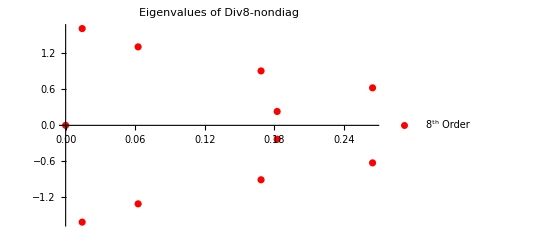

```mathematica
cplot8=ComplexListPlot[vals8,AspectRatio->1/GoldenRatio,PlotRange->Automatic,PlotLabel->"Eigenvalues of Div8-nondiag",PlotStyle->Red,PlotLegends->{"8^th Order"}]
```

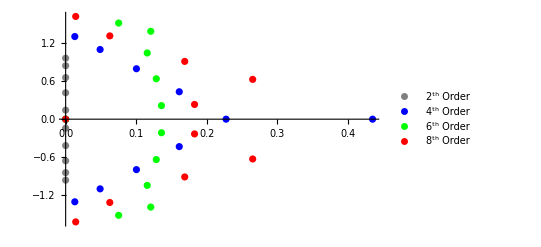

```mathematica
Show[cplot2, cplot4, cplot6, cplot8, AspectRatio->1/GoldenRatio,PlotRange->All]
```

```mathematica
(lvals8=Sort[Eigenvalues[N[DDIV8.grad8]]])//MatrixForm
(lvals6=Sort[Eigenvalues[N[DDIV6.grad6]]])//MatrixForm
(lvals4=Sort[Eigenvalues[N[DDIV4.grad4]]])//MatrixForm
(lvals2=Sort[Eigenvalues[N[DDIV2.grad2]]])//MatrixForm
```

(-4.07244
-2.81869
-2.67194
-2.01955
-1.95514
-1.3585
-1.03667
-0.665129
-0.383272
-0.134913
-2.08525×10^-17)

(-5.17792
-2.46243
-2.28116
-1.86205
-1.57628
-1.15551
-0.882301
-0.554001
-0.344707
-0.127715
1.50049×10^-16)

(-2.66327
-1.79364
-1.69222
-1.33812
-1.16785
-0.7943
-0.627242
-0.385554
-0.26316
-0.113283
4.07472×10^-16)

(-1.63191
-1.04512
-0.943575
-0.84777
-0.712836
-0.575441
-0.419651
-0.291369
-0.157626
-0.0787791
4.32117×10^-17)

```mathematica
eigenfunc=DSolve[{D[ψ[x],{x,2}]+(2l+2)/x ψ'[x]+k^2 ψ[x]==0},ψ[x],x]/.C[2]->0
```

{{ψ[x]→(ⅇ^(-ⅈ k x) C[1])/x}}

```mathematica
g=ψ[x]/.eigenfunc[[1]][[1]]
```

(ⅇ^(-ⅈ k x) C[1])/x

```mathematica
Reduce[x^(1/2 (-1-2 l)) BesselJ[1/2 (1+2 l),k x]==0&&l>0 &&x>0,k]
```

False

```mathematica
plot8=Plot[lvals8,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic},PlotLabel->"8th Order"];
```

```mathematica
plot6=Plot[lvals6,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic},PlotLabel->"6th Order"];
```

```mathematica
plot4=Plot[lvals4,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic},PlotLabel->"4th Order"];
```

```mathematica
(cvals4=Eigenvalues[div4.grad4]) // MatrixForm//N;
```

```mathematica
plot2=Plot[lvals2,{x,.2,1},PlotStyle->Black,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
plot4c=Plot[cvals4,{x,.2,1},PlotStyle->Blue,Axes->{False,True},AspectRatio->GoldenRatio,PlotRange->{{0,1},Automatic}];
```

```mathematica
Show[plot4c,plot4];
```

```mathematica
Show[plot0,plot4]
```

-Graphics-

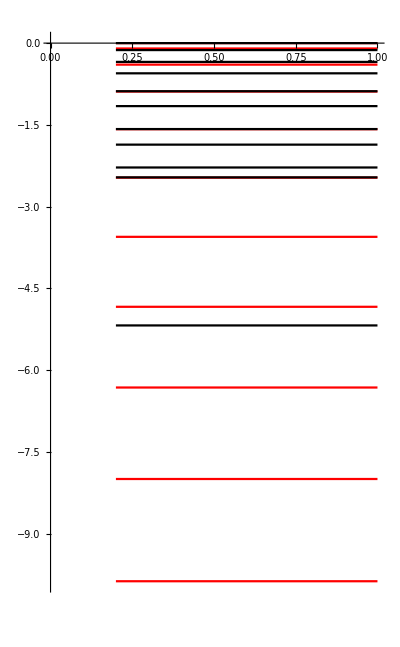

```mathematica
Show[plot0, plot6]
```

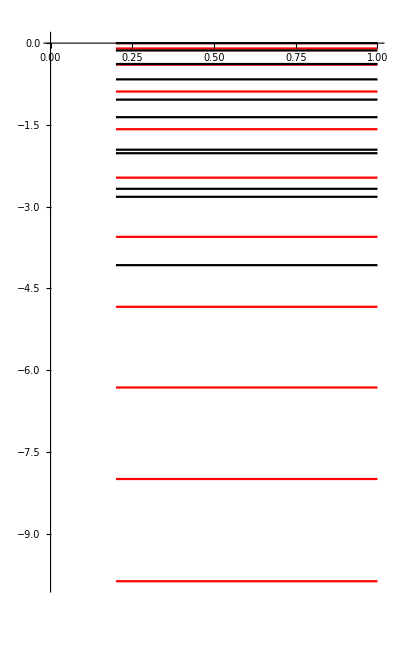

```mathematica
Show[plot0, plot8]
```

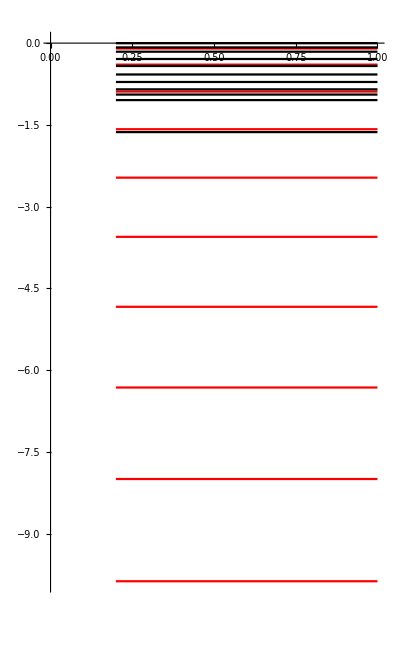

```mathematica
Show[plot0,plot2]
```

```mathematica
(vecs2=Eigensystem[N[DDIV6.grad6]])//MatrixForm;
```

```mathematica
vecs2[[1]]//MatrixForm
vecs2[[2]]//MatrixForm
```

(-5.17792
-2.46243
-2.28116
-1.86205
-1.57628
-1.15551
-0.882301
-0.554001
-0.344707
-0.127715
1.50049×10^-16)

(-0.977559 | -0.0811017 | 0.186249 | -0.0544813 | -0.00464377 | 0.0106422 | -0.00301859 | -0.000647779 | 0.000759781 | -0.000165459 | -0.0000662443
-0.517206 | -0.642166 | 0.228625 | 0.339345 | -0.313964 | -0.0271991 | 0.197371 | -0.0858162 | -0.0582893 | 0.0605351 | 0.000846369
0.847016 | 0.216805 | 0.202214 | -0.138211 | -0.222533 | 0.270862 | 0.0218693 | -0.199605 | 0.0852757 | 0.0580636 | -0.0414239
-0.500777 | -0.780205 | 0.14949 | 0.26187 | -0.0690668 | -0.0132579 | -0.124283 | 0.0713339 | 0.115878 | -0.101134 | -0.0210249
-0.854328 | -0.19339 | -0.382987 | 0.100433 | 0.213454 | -0.0607256 | -0.0132194 | -0.113162 | 0.0422652 | 0.101531 | -0.0404005
-0.368621 | -0.888626 | 0.0490222 | -0.00851972 | 0.178148 | 0.0907793 | -0.119556 | -0.0167013 | -0.090536 | 0.0805313 | 0.052486
0.796243 | 0.192283 | 0.526546 | -0.0230261 | 0.00300861 | -0.161889 | -0.0889047 | 0.0448258 | 0.0277753 | 0.1165 | -0.0277487
0.324291 | 0.824048 | 0.130674 | 0.3556 | -0.142893 | 0.0146488 | -0.194134 | -0.0447143 | -0.0263712 | 0.0269906 | 0.10251
0.669886 | 0.265842 | 0.564041 | 0.138792 | 0.29539 | -0.0712111 | 0.0472014 | -0.175495 | -0.0534234 | -0.120667 | -0.0201992
-0.357573 | -0.563087 | -0.319568 | -0.475576 | -0.22158 | -0.340969 | -0.0919847 | -0.189117 | 0.0315914 | -0.0567428 | 0.113912
0.402941 | 0.0784126 | 0.402941 | 0.0784125 | 0.402941 | 0.0784121 | 0.402943 | 0.0784499 | 0.403184 | 0.0788934 | 0.396448)

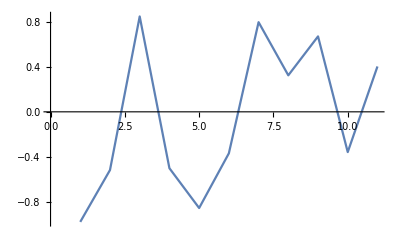

```mathematica
ListLinePlot[vecs2[[2]][[;;,1]]]
```

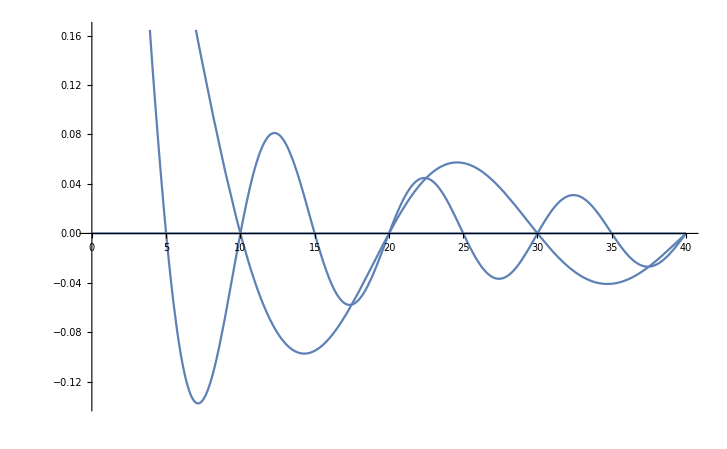

```mathematica
Plot[x^(1/2 (-1-2 l)) BesselJ[1/2 (1+2 l),kk[[1;;3]] x],{x,0,40}]
```